```mathematica
(* GENERAL DEFINITIONS *)
```

```mathematica
x[i_]:=Subscript[x,i]
α[i_]:=Subscript[α,i]
```

# Application: MMM with Random Effects Models

## (* Definition of the model *)

{0.1,9}

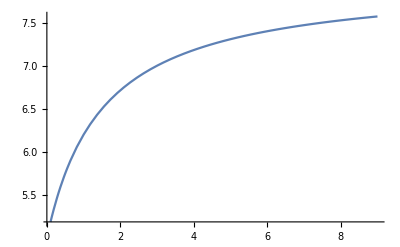

```mathematica
MM[x_,V_,K_]:=V*x/(x+K)+5
{V0,K0}={3,1.5};
{l,u}={0.1,3*V0}
Plot[MM[x,V0,K0],{x,l,u}]
```

# (* Making the simulations *)

```mathematica
S={{0.5,0.1},{0.1,0.4}};
σ2=0.001;
Det[S]
n=50;(* number of clusters *)
m=24; (* number of replicates under the same V0 and K0 *)

pointsx=Join[
Table[χ[[1]],{i,1,m/6}],
Table[χ[[1]]+(χ[[2]]-χ[[1]])/5,{i,1,m/6}],
Table[χ[[1]]+2*(χ[[2]]-χ[[1]])/5,{i,1,m/6}],
Table[χ[[1]]+3*(χ[[2]]-χ[[1]])/5,{i,1,m/6}],
Table[χ[[1]]+4*(χ[[2]]-χ[[1]])/5,{i,1,m/6}],
Table[χ[[1]]+5*(χ[[2]]-χ[[1]])/5,{i,1,m/6}]
]
simVK=RandomVariate[MultinormalDistribution[{V0,K0},S],n];
group=Table[i,{i,1,n},{j,1,m}];

sim=Transpose[Table[{{group[[j,i]],pointsx[[i]],
RandomVariate[
NormalDistribution[
MM[pointsx[[i]],simVK[[j,1]],simVK[[j,2]]],σ2
]
]}}
,{j,1,n},{i,1,m}]];

sim={};
Do[
AppendTo[sim,{group[[j,i]],pointsx[[i]],
Max[0,RandomVariate[
NormalDistribution[
MM[pointsx[[i]],simVK[[j,1]],simVK[[j,2]]],σ2
]
]]}]
,{j,1,n},{i,1,m}]
```

## (* Models from R fitting *)

```mathematica
f1[x_]:=α[0]+α[1]*x^{-0.5}+α[2]*x^{-0.5}*Log[x];
f2[x_]:=α[0]+α[1]*x^{-2}+α[2]*x^{-0.5};
f3[x_]:=α[0]+α[1]*x^{-1}+α[2]*x^{-0.5};
f4[x_]:=α[0]+α[1]*x^{-1}+α[2]*x^{-1}*Log[x];

Truemodel[x_]:=α[0]+α[1]*x^(-0.5)+α[2]*x^(-0.5)*Log[x]+α[3]*x^{-2}+α[4]*x^(-1)+α[5]*x^{-1}*Log[x];

(* Parameters of the model from R code *)
tmparam={Subscript[α, 0]->7.21887,Subscript[α, 1]->-8.25043,Subscript[α, 2]->2.58984,Subscript[α, 3]->-0.03916,Subscript[α, 4]->7.28339,Subscript[α, 5]->1.12841};
```

```mathematica
m=24;(* number of design points*)
G1=Transpose[
Table[D[f1[x[j]],i][[1]],{i,{α[0],α[1],α[2]}},{j,1,m}]
];
G2=Transpose[
Table[D[f2[x[j]],i][[1]],{i,{α[0],α[1],α[2]}},{j,1,m}]
];
G3=Transpose[
Table[D[f3[x[j]],i][[1]],{i,{α[0],α[1],α[2]}},{j,1,m}]
];
G4=Transpose[
Table[D[f4[x[j]],i][[1]],{i,{α[0],α[1],α[2]}},{j,1,m}]
];
Gt=Transpose[
Table[D[Truemodel[x[j]],i][[1]],{i,{α[0],α[1],α[2],α[3],α[4],α[5]}},{j,1,m}]
];
Gt//MatrixForm; 

at=Table[α[i]/.tmparam[[i+1]],{i,0,5}];
```

```mathematica
σ2=1;
Tt={
{  1.00, -1.00,  0.57, -0.51,   0.33,-0.53},
{-1.00,   1.00,-0.59,   0.53,-0.33,   0.55},
{   0.57,-0.59,   1.00,-0.16,   0.72,-0.23},
{-0.51,   0.53, -0.16,  1.00,   0.50,  1.00},
{   0.33,-0.33,   0.72,   0.50,   1.00,  0.45},{-0.53,   0.55,-0.23,   1.00,   0.45,  1.00}
};
```

```mathematica
Tt//MatrixForm
```

(1. | -1. | 0.57 | -0.51 | 0.33 | -0.53
-1. | 1. | -0.59 | 0.53 | -0.33 | 0.55
0.57 | -0.59 | 1. | -0.16 | 0.72 | -0.23
-0.51 | 0.53 | -0.16 | 1. | 0.5 | 1.
0.33 | -0.33 | 0.72 | 0.5 | 1. | 0.45
-0.53 | 0.55 | -0.23 | 1. | 0.45 | 1.)

```mathematica
minKL[des_,G_,Tt_,Gt_,at_]:=Module[
{
Σt,Σtinv,m=Length[des],Gaux,Gtaux,
desaux=Table[x[i]->des[[i]],{i,1,m}]
},
Gaux=G/.desaux;
Gtaux=Gt/.desaux;
Σt=Simplify[IdentityMatrix[m]+Gtaux.Tt.Transpose[Gtaux]];
Σtinv=Inverse[Σt];
1/(2*σ2)*(Transpose[Gtaux.at].Σtinv.Gtaux.at-Transpose[Gtaux.at].Σtinv.Gaux.Inverse[Transpose[Gaux].Σtinv.Gaux].Transpose[Gaux].Σtinv.Gtaux.at)
]
```

# KL-optimal designs

```mathematica
NN = 300; (* number of particles *)
```

```mathematica
(* 1 vs maximal *)


(* STEP 1.1: GENERATE INITIAL PARTICLES AND THEIR VELOCITIES *)
designsX = Table[Random[Real,{l,u}],{i,NN},{j,m}];

VelocPARAM = 0.5;
velocitiesX = Table[Random[Real,{-VelocPARAM,VelocPARAM}],{i,NN}, {j,m}];(* Velocity vector in each iteration *)

(* STEP 1.2 *)
localvalues=Table[minKL[designsX[[i]],G1,Tt,Gt,at],{i,1,NN}];(* We have to change Gi for each KL-optimal design *)
localBESTvalues=localvalues; (* localvalues are the best, because it is the first step *)

(* Step 1.3 Compute the best local and best global particle *)
localbestX=designsX;

PositionMax=Position[localBESTvalues,Max[localBESTvalues]][[1,1]];
globalbestX=localbestX[[PositionMax]];

c1X=1.5; c2X=1.5;
t=1;tmax=5000;
niter=5000;

Monitor[
Do[
(* Step 2.1 Computing the new particles *)
If[t>= 0.8*tmax, ω=0.2, ω=((0.2-0.95)/(0.8*tmax-1))*t+0.95-((0.2-0.95)/(0.8*tmax-1))];
R1X = Table[Random[],{j,m}];R2X = Table[Random[],{j,m}];
velocitiesX = ω*velocitiesX + 
c1X *Transpose[R1X *Transpose[localbestX- designsX ]]+
c2X *Transpose[R2X *Transpose[Table[globalbestX, {i,1,NN}] - designsX]];

(* Step 2.2 Updating the particles with the previous velocities *)
designsXprev = designsX; (* design step t-1 *)
designsX = designsXprev + velocitiesX;


(* Control of the designs *)
Do[
designsX[[i,j]]=Which[designsX[[i,j]] <l,designsX[[i,j]]=l,designsX[[i,j]] >u,designsX[[i,j]] =u,l≤designsX[[i,j]]≤u,designsX[[i,j]]] 
,{i,1,NN},{j,1,m}];

(* Step 2.3 Computing the criterion function for all new particles *)
localvalues=Table[minKL[designsX[[i]],G1,Tt,Gt,at],{i,1,NN}];   

(* Step 2.4: Updating best local particle *)
(* Cambio While por un For *)
Do[
If[
localvalues[[s]]> localBESTvalues[[s]],
localbestX[[s]] =designsX[[s]];
localBESTvalues[[s]]=localvalues[[s]],
Null
]
,{s,1,NN}];

(* Step 2.5: actualizamos global best *)
PositionMax = Position[localBESTvalues, Max[localBESTvalues]] [[1]][[1]];
globalbestX=localbestX[[PositionMax]];
,{t,1,niter}
],
{Round[Sort[globalbestX],0.0001]//MatrixForm,t,localBESTvalues[[PositionMax]],PositionMax,Max[localBESTvalues]-Min[localBESTvalues]}];


ξopt1=Round[Sort[globalbestX],0.0001]
Eff1opt=Max[localBESTvalues]
```

```mathematica
(* 2 vs maximal *)



designsX = Table[Random[Real,{l,u}],{i,NN},{j,m}];

VelocPARAM = 0.5;
velocitiesX = Table[Random[Real,{-VelocPARAM,VelocPARAM}],{i,NN}, {j,m}];

(* STEP 1.2 *)
localvalues=Table[minKL[designsX[[i]],G2,Tt,Gt,at],{i,1,NN}] ; 
localBESTvalues=localvalues; 
localbestX=designsX;

PositionMax=Position[localBESTvalues,Max[localBESTvalues]][[1,1]];
globalbestX=localbestX[[PositionMax]];

c1X=2; c2X=2;
t=1;tmax=2000;
niter=2000;

Monitor[
Do[
(* Step 2.1  *)
If[t>= 0.8*tmax, ω=0.2, ω=((0.2-0.95)/(0.8*tmax-1))*t+0.95-((0.2-0.95)/(0.8*tmax-1))];
R1X = Table[Random[],{j,m}];R2X = Table[Random[],{j,m}];
velocitiesX = ω*velocitiesX + 
c1X *Transpose[R1X *Transpose[localbestX- designsX ]]+
c2X *Transpose[R2X *Transpose[Table[globalbestX, {i,1,NN}] - designsX]];

(* Step 2.2 *)
designsXprev = designsX; (* design step t-1 *)
designsX = designsXprev + velocitiesX;

Do[
designsX[[i,j]]=Which[designsX[[i,j]] <l,designsX[[i,j]]=l,designsX[[i,j]] >u,designsX[[i,j]] =u,l≤designsX[[i,j]]≤u,designsX[[i,j]]] 
,{i,1,NN},{j,1,m}];

(* Step 2.3 *)
localvalues=Table[minKL[designsX[[i]],G2,Tt,Gt,at],{i,1,NN}];   

(* Step 2.4 *)
Do[
If[
localvalues[[s]]> localBESTvalues[[s]],
localbestX[[s]] =designsX[[s]];
localBESTvalues[[s]]=localvalues[[s]],
Null
]
,{s,1,NN}];

(* Step 2.5 *)
PositionMax = Position[localBESTvalues, Max[localBESTvalues]] [[1]][[1]];
globalbestX=localbestX[[PositionMax]];
,{t,1,niter}
],
{Round[Sort[globalbestX],0.0001]//MatrixForm,t,localBESTvalues[[PositionMax]],PositionMax,Max[localBESTvalues]-Min[localBESTvalues]}];



ξopt2=Round[Sort[globalbestX],0.0001]
Eff2opt=Max[localBESTvalues]
```

```mathematica
(* 3 vs maximal *)


(* STEP 1.1*)
designsX = Table[Random[Real,{l,u}],{i,NN},{j,m}];

VelocPARAM = 0.5;
velocitiesX = Table[Random[Real,{-VelocPARAM,VelocPARAM}],{i,NN}, {j,m}];

(* STEP 1.2 *)
localvalues=Table[minKL[designsX[[i]],G3,Tt,Gt,at],{i,1,NN}] ; (* We have to change Gi for each KL-optimal design *)
localBESTvalues=localvalues; (* localvalues are the best, because it is the first step *)

(* Step 1.3 *)
localbestX=designsX;

PositionMax=Position[localBESTvalues,Max[localBESTvalues]][[1,1]];
globalbestX=localbestX[[PositionMax]];

c1X=2; c2X=2;
t=1;tmax=2000;
niter=2000;

Monitor[
Do[
(* Step 2.1 *)
If[t>= 0.8*tmax, ω=0.2, ω=((0.2-0.95)/(0.8*tmax-1))*t+0.95-((0.2-0.95)/(0.8*tmax-1))];
R1X = Table[Random[],{j,m}];R2X = Table[Random[],{j,m}];
velocitiesX = ω*velocitiesX + 
c1X *Transpose[R1X *Transpose[localbestX- designsX ]]+
c2X *Transpose[R2X *Transpose[Table[globalbestX, {i,1,NN}] - designsX]];

(* Step 2.2 *)
designsXprev = designsX; (* design step t-1 *)
designsX = designsXprev + velocitiesX;

Do[
designsX[[i,j]]=Which[designsX[[i,j]] <l,designsX[[i,j]]=l,designsX[[i,j]] >u,designsX[[i,j]] =u,l≤designsX[[i,j]]≤u,designsX[[i,j]]] 
,{i,1,NN},{j,1,m}];

(* Step 2.3 *)
localvalues=Table[minKL[designsX[[i]],G3,Tt,Gt,at],{i,1,NN}];   (* We have to change Gi for each KL-optimal design *)

(* Step 2.4 *)
Do[
If[
localvalues[[s]]> localBESTvalues[[s]],
localbestX[[s]] =designsX[[s]];
localBESTvalues[[s]]=localvalues[[s]],
Null
]
,{s,1,NN}];

(* Step 2.5 *)
PositionMax = Position[localBESTvalues, Max[localBESTvalues]] [[1]][[1]];
globalbestX=localbestX[[PositionMax]];
,{t,1,niter}
],
{Round[Sort[globalbestX],0.0001]//MatrixForm,t,localBESTvalues[[PositionMax]],PositionMax,Max[localBESTvalues]-Min[localBESTvalues]}];



ξopt3=Sort[globalbestX]
Eff3opt=Max[localBESTvalues]
```

```mathematica
(* 4 vs maximal *)


(* STEP 1.1 *)
designsX = Table[Random[Real,{l,u}],{i,NN},{j,m}];

VelocPARAM = 0.5;
velocitiesX = Table[Random[Real,{-VelocPARAM,VelocPARAM}],{i,NN}, {j,m}];

(* STEP 1.2 *)
localvalues=Table[minKL[designsX[[i]],G4,Tt,Gt,at],{i,1,NN}] ; (* We have to change Gi for each KL-optimal design *)
localBESTvalues=localvalues; 

(* Step 1.3  *)
localbestX=designsX;

PositionMax=Position[localBESTvalues,Max[localBESTvalues]][[1,1]];
globalbestX=localbestX[[PositionMax]];

c1X=2; c2X=2;
t=1;tmax=2000;
niter=2000;

Monitor[
Do[
(* Step 2.1  *)
If[t>= 0.8*tmax, ω=0.2, ω=((0.2-0.95)/(0.8*tmax-1))*t+0.95-((0.2-0.95)/(0.8*tmax-1))];
R1X = Table[Random[],{j,m}];R2X = Table[Random[],{j,m}];
velocitiesX = ω*velocitiesX + 
c1X *Transpose[R1X *Transpose[localbestX- designsX ]]+
c2X *Transpose[R2X *Transpose[Table[globalbestX, {i,1,NN}] - designsX]];

(* Step 2.2  *)
designsXprev = designsX; (* design step t-1 *)
designsX = designsXprev + velocitiesX;

Do[
designsX[[i,j]]=Which[designsX[[i,j]] <l,designsX[[i,j]]=l,designsX[[i,j]] >u,designsX[[i,j]] =u,l≤designsX[[i,j]]≤u,designsX[[i,j]]] 
,{i,1,NN},{j,1,m}];

(* Step 2.3  *)
localvalues=Table[minKL[designsX[[i]],G4,Tt,Gt,at],{i,1,NN}];  

(* Step 2.4 *)
Do[
If[
localvalues[[s]]> localBESTvalues[[s]],
localbestX[[s]] =designsX[[s]];
localBESTvalues[[s]]=localvalues[[s]],
Null
]
,{s,1,NN}];

(* Step 2.5 *)
PositionMax = Position[localBESTvalues, Max[localBESTvalues]] [[1]][[1]];
globalbestX=localbestX[[PositionMax]];
,{t,1,niter}
],
{Round[Sort[globalbestX],0.0001]//MatrixForm,t,localBESTvalues[[PositionMax]],PositionMax,Max[localBESTvalues]-Min[localBESTvalues]}];

ξopt4=Sort[globalbestX]
Eff4opt=Max[localBESTvalues]
```

```mathematica
(* Definition of min Eff criterion *)


Eff1[des_]:=minKL[des,G1,Tt,Gt,at]/Eff1opt
Eff2[des_]:=minKL[des,G2,Tt,Gt,at]/Eff2opt
Eff3[des_]:=minKL[des,G3,Tt,Gt,at]/Eff3opt
Eff4[des_]:=minKL[des,G4,Tt,Gt,at]/Eff4opt
minEff[des_]:=Min[Eff1[des],Eff2[des],Eff3[des],Eff4[des]] (* Definition of the criterion of minimum efficiency *)
```

# PSO maxminEff

```mathematica
NN = 300; 



(* STEP 1.1: GENERATE INITIAL PARTICLES AND THEIR VELOCITIES *)
designsX = Table[Random[Real,{l,u}],{i,NN},{j,m}];

VelocPARAM = 1;
velocitiesX = Table[Random[Real,{-VelocPARAM,VelocPARAM}],{i,NN}, {j,m}];

(* STEP 1.2 *)
localvalues=Table[minEff[designsX[[i]]],{i,1,NN}];
localBESTvalues=localvalues; 

(* Step 1.3 *)
localbestX=designsX;

PositionMax=Position[localBESTvalues,Max[localBESTvalues]][[1,1]];
globalbestX=localbestX[[PositionMax]];


c1X=1.5; c2X=1.5;
t=1;tmax=3000;
niter=3000;

Monitor[
Do[
(* Step 2.1 *)
If[t>= 0.8*tmax, ω=0.2, ω=((0.2-0.95)/(0.8*tmax-1))*t+0.95-((0.2-0.95)/(0.8*tmax-1))];
R1X = Table[Random[],{j,m}];R2X = Table[Random[],{j,m}];
velocitiesX = ω*velocitiesX + 
c1X *Transpose[R1X *Transpose[localbestX- designsX ]]+
c2X *Transpose[R2X *Transpose[Table[globalbestX, {i,1,NN}] - designsX]];

(* Step 2.2  *)
designsXprev = designsX; 
designsX = designsXprev + velocitiesX;


Do[
designsX[[i,j]]=Which[designsX[[i,j]] <l,designsX[[i,j]]=l,designsX[[i,j]] >u,designsX[[i,j]] =u,l≤designsX[[i,j]]≤u,designsX[[i,j]]] 
,{i,1,NN},{j,1,m}];

(* Step 2.3 *)
localvalues=Table[minEff[designsX[[i]]],{i,1,NN}];

(* Step 2.4 *)
(* Cambio While por un For *)
Do[
If[
localvalues[[s]]> localBESTvalues[[s]],
localbestX[[s]] =designsX[[s]];
localBESTvalues[[s]]=localvalues[[s]],
Null
]
,{s,1,NN}];

(* Step 2.5 *)
PositionMax = Position[localBESTvalues, Max[localBESTvalues]] [[1]][[1]];
globalbestX=localbestX[[PositionMax]];
,{t,1,niter}
],
{Round[Sort[globalbestX],0.0001]//MatrixForm,t,localBESTvalues[[PositionMax]],PositionMax,Max[localBESTvalues]-Min[localBESTvalues]}];

Sort[globalbestX]
Eff1[minmaxKLopt]
Eff2[minmaxKLopt]
Eff3[minmaxKLopt]
Eff4[minmaxKLopt]
```